```mathematica
(*This is how we write notes!*)

(*Define Variables*)
x=1; (*Use ";" to not display an output*)
y=2;

x+y (*Without the ";" this will display the result*)
(*Enter+Shift To evaluate Cell*)
```

3

```mathematica
x= 2 (*You can redefine values*)
```

```mathematica
2

(*You can have any names. Also, definitions can include undefined variables which you can define later. When defined, all instances of an undefined variable, which would otherwise be blue would turn to black*)
a=b+c-x
b=3
```

2

-1+b+c

3

```mathematica
(*Values are exact! Yay... No decimals*)
```

```mathematica
1+2/5
```

7/5

```mathematica
(*WRITING FUNCTIONS!*)
(* This is how you define functions: f(x_):= ... note the _ after that x? That is important to make it from a previously defined value x. Simply saying f(x) would mean something wierd which idk. JUST USE "_" and :=*)
```

```mathematica
f[x_]:=g[x]+3 
g[x_]:=x^2+2
```

```mathematica
f[3]
```

14

You can change cell Formats too! Click on Format and change Style to 
Text/Title/Code/Input ... Anything you like


You can write special symbols with “\[name]” like \[Degree]

```mathematica
a°=90
```

90

```mathematica
CosDegrees[a°]
```

0

```mathematica
(*Args and Kwargs source: https://mathematica.stackexchange.com/questions/201112/naming-arguments-in-wolfram-functions*)
```

```mathematica
h[x_, OptionValue[y_]]:=x+y
```

```mathematica
h[5]
```

h[5]

```mathematica
h[5]
```

```mathematica
h[5]
```

h[5]

{1,2}

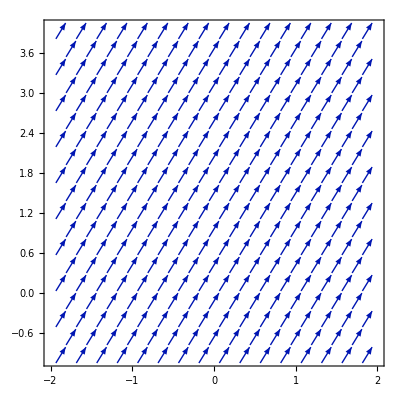

Point[{1,2}]

PlotPoints

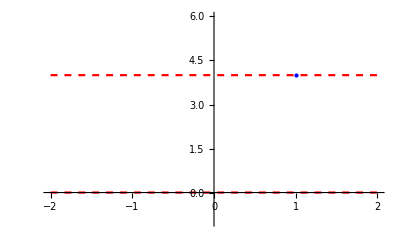

```mathematica
v={1,2}
VectorPlot[v, {x, -2,2},{y,-1,4}]
Point[v]
PlotPoints
Plot[{4,0},{x,-2,2},Epilog->{Blue,PointSize@Large,Point[{1,4}]},PlotStyle->{{Red,Dashed,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},PlotRange->{-1,6}]
```

```mathematica
M={{3,4},{1,2}}
MatrixForm[M]
```

{{3,4},{1,2}}

(3 | 4
1 | 2)